# Half Rod, Albedo Problem, Isotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2015 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)

## Analytic solutions

### Half rod reflectance/albedo (R)

```mathematica
Clear[α,g];R[α_]:=2(-α/2-√(1-α)+1)/α
```

```mathematica
Series[R[α],{α,0,5}]
```

α/4+α^2/8+(5 α^3)/64+(7 α^4)/128+(21 α^5)/512+O[α]^6

```mathematica
R[α_,n_]:=α^n(SeriesCoefficient[R[A],{A,0,n}]/.A->α)
```

### Internal distribution, ‘radiance’

```mathematica
LR[x_,α_,Σt_]:=ⅇ^(-√(1-α) Σt x)
```

```mathematica
LL[x_,α_,Σt_]:=(α Exp[-Σt √(1-α)x])/(-α+2 √(1-α)+2)
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_]:=LR[x,α,Σt]+LL[x,α,Σt]
```

### n-th collided fluence

```mathematica
ϕ[x_,α_,Σt_,n_]:=α^n(SeriesCoefficient[ϕ[x,A,Σt],{A,0,n}]/.A->α)
```

### Moments

```mathematica
ϕm[α_,Σt_,k_]:=(2 (1-α)^(-1-k/2) (-1+√(1-α)+α) Σt^(-1-k) Gamma[1+k])/α
```

Only accurate for n even

```mathematica
ϕm[α_,Σt_,k_,n_]:=α^n(2 (-1)^n Σt^(-1-k) Gamma[1+k] (-(2+n) Gamma[(1-k)/2]-((k+n) Binomial[-k/2,1+n]+2 (2+n) Binomial[-k/2,2+n]) Gamma[-1/2-k/2-n] Gamma[2+n]))/(Gamma[-1/2-k/2-n] Gamma[3+n])
```

## load MC data

```mathematica
ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
fs=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
```

```mathematica
alphas=Union[#[[1]]&/@simulations]
```

{0.1,0.3,0.5,0.7,0.9,0.95,0.98,0.99,0.999}

```mathematica
muts=Union[#[[2]]&/@simulations]
```

{1,3}

## Halfrod Albedo

```mathematica
MCalbedo[f_]:=Module[{data,α},
data=Import[f,"Table"];
α=data[[2,3]];
{α,data[[3,3]]}
]
```

```mathematica
MCalbedos=Table[MCalbedo[f],{f,fs}]
```

{{0.1,0.0262874},{0.1,0.0262874},{0.3,0.0888128},{0.3,0.0888128},{0.5,0.17156},{0.5,0.17156},{0.7,0.291991},{0.7,0.291991},{0.95,0.633904},{0.95,0.633904},{0.98,0.751703},{0.98,0.751703},{0.999,0.938793},{0.999,0.938793},{0.99,0.818082},{0.99,0.818082},{0.9,0.519448},{0.9,0.519448}}

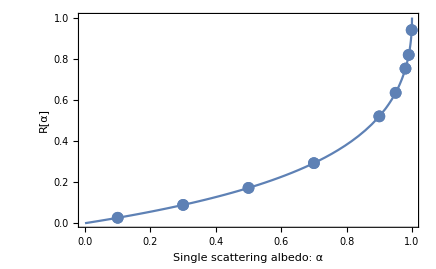

```mathematica
Clear[α];vizrodalbedoiso=Show[
Plot[R[c],{c,0,1}],
ListPlot[MCalbedos]
,Frame->True,FrameLabel->{{"R[α]",},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half rod"}}
]
```

## Compare Deterministic and MC

```mathematica
Clear[alpha,Σt];
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];

densmom=data[[11]];

pointsCL = data[[7]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,maxx,Σt];
pointsCR = data[[9]];
plotpointsCR=ppoints[pointsCR,dx,maxx,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}}
];

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
];

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Semi-infinite rod, albedo problem, isotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
];
Show[GraphicsGrid[{{plotϕ},{plotLL},{plotLR}}],ImageSize->500]
,{α,alphas},{Σt,muts}]
```

### n-th collided albedo

```mathematica
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
Rs=N[{data[[5]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[R[α,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
,{α,alphas},{Σt,muts}]
```

```mathematica
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
ϕmoments=N[{data[[13+n]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[Quiet[N[ϕm[α,Σt,k,n]]],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
,{α,alphas},{Σt,muts},{n,Range[numcollorders]}]
```

### Compare moments of ϕ

Divide these results, which are collision density moments, by Σt to produce radiance/fluence moments:

```mathematica
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
ϕmoments=N[{data[[11]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[ϕm[α,Σt,k],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
,{α,alphas},{Σt,muts}]
```

### N-th order Radiance/Angular flux

```mathematica
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Clear[c];LnR=FullSimplify[SeriesCoefficient[LR[x,c,Σt],{c,0,n}] α^n];
Show[
ListPlot[ppoints[nthR[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LnR,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, isotropic scattering, L_+[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
,{α,alphas},{Σt,muts},{n,Range[numcollorders]}]
```

### N-th order Fluence / scalar flux

```mathematica
Manipulate[
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Clear[c];ϕn=FullSimplify[SeriesCoefficient[ϕ[x,c,Σt],{c,0,n}] α^n];
Show[
ListPlot[ppoints[nthR[[n+1]]+nthL[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕn,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, isotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
,{α,alphas},{Σt,muts},{n,Range[numcollorders]}]
```